## Input

### Derivatives of Shape Function

```mathematica
hhp=({{-1.5, -0.5, 0.5}, {2, 0, -2}, {-0.5, 0.5, 1.5}});
(*hhp=Transpose[hhp];*)
```

### Weight Function

```mathematica
wj=({{1.0/3}, {4.0/3}, {1.0/3}});
```

### Beam Length and Cross-Section Constants

```mathematica
L=10;
EA=10^4;
GA=10^4;
EI=10^2;
(*EA=70*10^9;
GA=5.*27*10^9/6.;
EI=70*10^9/12.;*)
Stif0=Table[0,{i,6},{j,6}];
Stif0[[1,1]]=1.0*10^4;
Stif0[[2,2]]=1.0*10^4;
Stif0[[3,3]]=1.0*10^4;
Stif0[[4,4]]=1.0*10^4;
Stif0[[5,5]]=1.0*10^2;
Stif0[[6,6]]=1.0*10^2;
```

### Jacobian and Initial Value

```mathematica
Jaco=L/2;
uuNf={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0}};
(*uuNf={{0.},{0},{0},{0},{0},{0},{-0.02049828886732387},{0},{0.39148964058766911},{0},{-0.15716032849168254},{0},{-0.16373355452761346},{0},{1.55791055309517068},{0},{-0.31480662768318024},{0}};(*Dymore converged values*)
uuNf={{0.},{0},{0},{0},{0},{0},{-3.89928706730006134*10^-3},{0},{0.17094403785857842},{0},{6.83843261387723222*10^-2},{0},{-3.11396882412181171*10^-2},{0},{0.68271172942293523},{0},{-0.13680863815958869},{0}};(*BDyn converged values*)*)
uuN0={{0.},{0},{0},{0},{0},{0},{5.},{0},{0},{0},{0},{0},{10.},{0},{0},{0},{0},{0}};
Fext={{0.},{0},{0},{0},{0},{0},{0.},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-3.14159*10^0},{0}};
ui=Table[0,{i,18},{j,1}];
tolx=1.0*10^-6;
FmL=3.14159*10^0;
```

## Utilities

```mathematica
Tilde[v1_,v2_,v3_]:=Module[{m12,m13,m21,m23,m31,m32},
m12=-v3;m13=v2;
m21=v3;m23=-v1;
m31=-v2;m32=v1;
{{0,m12,m13},{m21,0,m23},{m31,m32,0}}]
```

## CRV Functions

### CRV Compose 0

```mathematica
CrvCompose0[cc1_,cc2_,cc3_,c01_,c02_,c03_]:=Module[{pp0,pp1=cc1,pp2=cc2,pp3=cc3,qq0,qq1=c01,qq2=c02,qq3=c03,tr1,tr2,dd1,dd2,c1,c2,c3},
pp0=2.0-(pp1*pp1+pp2*pp2+pp3*pp3)/8;
qq0=2.0-(qq1*qq1+qq2*qq2+qq3*qq3)/8;
tr1=(4-pp0)*(4-qq0);
tr2=pp0*qq0-pp1*qq1-pp2*qq2-pp3*qq3;
dd1=tr1+tr2;
dd2=tr1-tr2;
If[dd1>dd2,tr1=4/dd1,tr1=-4/dd2];
c1=tr1*(pp1*qq0+pp0*qq1-pp3*qq2+pp2*qq3);
c2=tr1*(pp2*qq0+pp3*qq1+pp0*qq2-pp1*qq3);
c3=tr1*(pp3*qq0-pp2*qq1+pp1*qq2+pp0*qq3);
{{c1},{c2},{c3}}];
```

### CRV Compose 1

```mathematica
CrvCompose1[cc1_,cc2_,cc3_,c01_,c02_,c03_]:=Module[{pp0,pp1=-cc1,pp2=-cc2,pp3=-cc3,qq0,qq1=c01,qq2=c02,qq3=c03,tr1,tr2,dd1,dd2,c1,c2,c3},
pp0=2.0-(pp1*pp1+pp2*pp2+pp3*pp3)/8;
qq0=2.0-(qq1*qq1+qq2*qq2+qq3*qq3)/8;
tr1=(4-pp0)*(4-qq0);
tr2=pp0*qq0-pp1*qq1-pp2*qq2-pp3*qq3;
dd1=tr1+tr2;
dd2=tr1-tr2;
If[dd1>dd2,tr1=4/dd1,tr1=-4/dd2];
c1=tr1*(pp1*qq0+pp0*qq1-pp3*qq2+pp2*qq3);
c2=tr1*(pp2*qq0+pp3*qq1+pp0*qq2-pp1*qq3);
c3=tr1*(pp3*qq0-pp2*qq1+pp1*qq2+pp0*qq3);
{{c1},{c2},{c3}}];
```

### CRV Matrix R

```mathematica
CrvMatrixR[cc1_,cc2_,cc3_]:=Module[{c0,c1=cc1/4,c2=cc2/4,c3=cc3/4,tr0,R0,R1,R2,R3,R4,R5,R6,R7,R8},
c0=0.5*(1-c1*c1-c2*c2-c3*c3);
tr0=1-c0;
tr0=2/(tr0*tr0);
R0=tr0*(c1*c1+c0*c0)-1;
R1=tr0*(c1*c2+c0*c3);
R2=tr0*(c1*c3-c0*c2);
R3=tr0*(c1*c2-c0*c3);
R4=tr0*(c2*c2+c0*c0)-1;
R5=tr0*(c2*c3+c0*c1);
R6=tr0*(c1*c3+c0*c2);
R7=tr0*(c2*c3-c0*c1);
R8=tr0*(c3*c3+c0*c0)-1;
{{R0,R3,R6},{R1,R4,R7},{R2,R5,R8}}];
```

### CRV Matrix H

```mathematica
CrvMatrixH[cc1_,cc2_,cc3_]:=Module[{cf1=cc1/4,cf2=cc2/4,cf3=cc3/4,cq,ocq,aa,cb0,cb1,cb2,cb3,H0,H1,H2,H3,H4,H5,H6,H7,H8},
cq=cf1*cf1+cf2*cf2+cf3*cf3;
ocq=1+cq;
aa=2*ocq*ocq;
cb0=2*(1-cq)/aa;
cb1=cc1/aa;
cb2=cc2/aa;
cb3=cc3/aa;
H0=cb1*cf1+cb0;
H1=cb2*cf1+cb3;
H2=cb3*cf1-cb2;
H3=cb1*cf2-cb3;
H4=cb2*cf2+cb0;
H5=cb3*cf2+cb1;
H6=cb1*cf3+cb2;
H7=cb2*cf3-cb1;
H8=cb3*cf3+cb0;
{{H0,H3,H6},{H1,H4,H7},{H2,H5,H8}}];
```

## GLL Shape Function

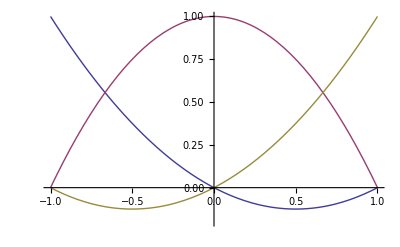

```mathematica
norder=2;
GLL1=-1.0;
GLL2=0.0;
GLL3=1.0;
GL1=-Sqrt[3]/3.0;
GL2=Sqrt[3]/3.0;
hh1[s_]:=Piecewise[{{1,s==GLL1},{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL1]*(s-GLL1)),GLL1<s≤1}}];
hh2[s_]:=Piecewise[{{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL2]*(s-GLL2)),-1≤s<GLL2},{1,s==GLL2},{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL2]*(s-GLL2)),GLL2<s≤1}}];
hh3[s_]:=Piecewise[{{(1/2 (-1+s^2) (0+6 s))/(norder*(norder+1)*LegendreP[2,GLL3]*(s-GLL3)),-1≤s<GLL3},{1,s==GLL3}}];
Plot[{hh1[s],hh2[s],hh3[s]},{s,-1,1},PlotRange->{{-1,1},{-0.2,1}}]
```

## First Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm;
E10N2//MatrixForm;
E10N3//MatrixForm;
```

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm;
E1N2//MatrixForm;
E1N3//MatrixForm;
```

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]];
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]];
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]];
```

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm;
RR0N2//MatrixForm;
RR0N3//MatrixForm;
```

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
```

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm;
```

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]]; 
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]]; 
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]];
```

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm;
rrpN2 // MatrixForm;
rrpN3 // MatrixForm;
```

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN2.rrpN3;
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm;
```

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm;
kapaN2 // MatrixForm;
kapaN3 // MatrixForm;
```

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cet*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cet*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cet*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cet*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cet*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cet*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm;
FcN2//MatrixForm;
FcN3//MatrixForm;
FdN1//MatrixForm;
FdN2//MatrixForm;
FdN3//MatrixForm;
```

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
(*Check Output*)
StifN3//MatrixForm
```

(10000. | 0. | 0. | 0. | 0. | 0.
0. | 10000. | 0. | 0. | 0. | 0.
0. | 0. | 10000. | 0. | 0. | 0.
0. | 0. | 0. | 10000. | 0. | 0.
0. | 0. | 0. | 0. | 100. | 0.
0. | 0. | 0. | 0. | 0. | 100.)

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
temp66//MatrixForm
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 16666.7 | 0.
0. | 0. | 0. | 0. | 0. | 16666.7)

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,66666.7,0.},{0.,0.,0.,0.,0.,66666.7}}

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(2333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 0. | 0. | 333.333 | 0. | 0. | 0. | 0. | 0.
0. | 2333.33 | 0. | 0. | 0. | 5000. | 0. | -2666.67 | 0. | 0. | 0. | 6666.67 | 0. | 333.333 | 0. | 0. | 0. | -1666.67
0. | 0. | 2333.33 | 0. | -5000. | 0. | 0. | 0. | -2666.67 | 0. | -6666.67 | 0. | 0. | 0. | 333.333 | 0. | 1666.67 | 0.
0. | 0. | 0. | 2333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 0. | 0. | 333.333 | 0. | 0.
0. | 0. | -5000. | 0. | 16690. | 0. | 0. | 0. | 6666.67 | 0. | -26.6667 | 0. | 0. | 0. | -1666.67 | 0. | 3.33333 | 0.
0. | 5000. | 0. | 0. | 0. | 16690. | 0. | -6666.67 | 0. | 0. | 0. | -26.6667 | 0. | 1666.67 | 0. | 0. | 0. | 3.33333
-2666.67 | 0. | 0. | 0. | 0. | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 0. | 0.
0. | -2666.67 | 0. | 0. | 0. | -6666.67 | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 6666.67
0. | 0. | -2666.67 | 0. | 6666.67 | 0. | 0. | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | -6666.67 | 0.
0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 0. | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0.
0. | 0. | -6666.67 | 0. | -26.6667 | 0. | 0. | 0. | 0. | 0. | 66720. | 0. | 0. | 0. | 6666.67 | 0. | -26.6667 | 0.
0. | 6666.67 | 0. | 0. | 0. | -26.6667 | 0. | 0. | 0. | 0. | 0. | 66720. | 0. | -6666.67 | 0. | 0. | 0. | -26.6667
333.333 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 0. | 0. | 2333.33 | 0. | 0. | 0. | 0. | 0.
0. | 333.333 | 0. | 0. | 0. | 1666.67 | 0. | -2666.67 | 0. | 0. | 0. | -6666.67 | 0. | 2333.33 | 0. | 0. | 0. | -5000.
0. | 0. | 333.333 | 0. | -1666.67 | 0. | 0. | 0. | -2666.67 | 0. | 6666.67 | 0. | 0. | 0. | 2333.33 | 0. | 5000. | 0.
0. | 0. | 0. | 333.333 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 0. | 0. | 2333.33 | 0. | 0.
0. | 0. | 1666.67 | 0. | 3.33333 | 0. | 0. | 0. | -6666.67 | 0. | -26.6667 | 0. | 0. | 0. | 5000. | 0. | 16690. | 0.
0. | -1666.67 | 0. | 0. | 0. | 3.33333 | 0. | 6666.67 | 0. | 0. | 0. | -26.6667 | 0. | -5000. | 0. | 0. | 0. | 16690.)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
elk[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
elk[[i,j]]=0;
];];
For[i=1,i≤6,i++,
elk[[i,i]]=1;];
elk//MatrixForm;
```

```mathematica
For[i=1,i≤6,i++,
elf[[i,1]]=0.0;
];
elf=elf+Fext;
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
-3.14159
0.)

```mathematica
Norm[elf]
```

3.14159

#### Solve elk.x=elf

```mathematica
ui=Table[0,{i,18},{j,1}];
ui=Inverse[elk].elf;
ui//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.392699
0.
-0.157079
0.
0.
0.
1.57079
0.
-0.314159
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=ui[[(i-1)*6+j,1]];}];
}];
```

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
For[i=1,i≤3,i++,
{temp31=CrvCompose0[ui[[(i-1)*6+4,1]],ui[[(i-1)*6+5,1]],ui[[(i-1)*6+6,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+3+j,1]]=temp31[[j,1]];}
];}
];
uuNf//MatrixForm
NumberForm[uuNf,17]
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.392699
0.
-0.157079
0.
0.
0.
1.57079
0.
-0.314159
0.)

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.3926987499999112},{0.},{-0.1570794999999644},{0.},{0.},{0.},{1.570794999999644},{0.},{-0.3141589999999288},{0.}}

## Second Iteration

### (*Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### Compute E10

```mathematica
E10N1=Table[0,{i,1,3},{j,1}];
Do[E10N1[[1,1]]=E10N1[[1,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N1[[2,1]]=E10N1[[2,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N1[[3,1]]=E10N1[[3,1]]+hhp[[i,1]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N2=Table[0,{i,1,3},{j,1}];
Do[E10N2[[1,1]]=E10N2[[1,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N2[[2,1]]=E10N2[[2,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N2[[3,1]]=E10N2[[3,1]]+hhp[[i,2]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N3=Table[0,{i,1,3},{j,1}];
Do[E10N3[[1,1]]=E10N3[[1,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+1,1]],{i,3}]
Do[E10N3[[2,1]]=E10N3[[2,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+2,1]],{i,3}]
Do[E10N3[[3,1]]=E10N3[[3,1]]+hhp[[i,3]]*uuN0[[(i-1)*6+3,1]],{i,3}]
E10N1=E10N1/Jaco;
E10N2=E10N2/Jaco;
E10N3=E10N3/Jaco;
E10N1//MatrixForm
E10N2//MatrixForm
E10N3//MatrixForm
```

(1.
0.
0.)

(1.
0.
0.)

(1.
0.
0.)

### Compute E1

```mathematica
E1N1=Table[0,{i,1,3},{j,1}];
Do[E1N1[[1,1]]=E1N1[[1,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N1[[2,1]]=E1N1[[2,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N1[[3,1]]=E1N1[[3,1]]+hhp[[i,1]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N1=E1N1/Jaco+E10N1;
E1N2=Table[0,{i,1,3},{j,1}];
Do[E1N2[[1,1]]=E1N2[[1,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N2[[2,1]]=E1N2[[2,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N2[[3,1]]=E1N2[[3,1]]+hhp[[i,2]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N2=E1N2/Jaco+E10N2;
E1N3=Table[0,{i,1,3},{j,1}];
Do[E1N3[[1,1]]=E1N3[[1,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+1,1]],{i,3}]
Do[E1N3[[2,1]]=E1N3[[2,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+2,1]],{i,3}]
Do[E1N3[[3,1]]=E1N3[[3,1]]+hhp[[i,3]]*uuNf[[(i-1)*6+3,1]],{i,3}]
E1N3=E1N3/Jaco+E10N3;
E1N1//MatrixForm
E1N2//MatrixForm
E1N3//MatrixForm
```

(1.
0.
1.11022×10^-16)

(1.
0.
0.157079)

(1.
0.
0.314159)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
E1v3GL[s_]:=hh1[s]*E1N1[[3,1]]+hh2[s]*E1N2[[3,1]]+hh3[s]*E1N3[[3,1]];
E1v3GL[GL1]
E1v3GL[GL2]
```

0.0663896

0.247769

### Compute RR0

#### Compose ccc and cc0

```mathematica
ccN1=CrvCompose0[uuNf[[4,1]],uuNf[[5,1]],uuNf[[6,1]],uuN0[[4,1]],uuN0[[5,1]],uuN0[[6,1]]]
ccN2=CrvCompose0[uuNf[[10,1]],uuNf[[11,1]],uuNf[[12,1]],uuN0[[10,1]],uuN0[[11,1]],uuN0[[12,1]]]
ccN3=CrvCompose0[uuNf[[16,1]],uuNf[[17,1]],uuNf[[18,1]],uuN0[[16,1]],uuN0[[17,1]],uuN0[[18,1]]]
```

{{0.},{0.},{0.}}

{{0.},{-0.157079},{0.}}

{{0.},{-0.314159},{0.}}

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
ccv2GL[s_]:=hh1[s]*ccN1[[2,1]]+hh2[s]*ccN2[[2,1]]+hh3[s]*ccN3[[2,1]];
ccv2GL[GL1]
ccv2GL[GL2]
```

-0.0663896

-0.247769

#### Compute CRV Matrix R

```mathematica
RR0N1=CrvMatrixR[ccN1[[1,1]],ccN1[[2,1]],ccN1[[3,1]]];
RR0N2=CrvMatrixR[ccN2[[1,1]],ccN2[[2,1]],ccN2[[3,1]]];
RR0N3=CrvMatrixR[ccN3[[1,1]],ccN3[[2,1]],ccN3[[3,1]]];
RR0N1//MatrixForm
RR0N2//MatrixForm
RR0N3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(0.987701 | 0. | -0.156355
0. | 1. | 0.
0.156355 | 0. | 0.987701)

(0.951255 | 0. | -0.308405
0. | 1. | 0.
0.308405 | 0. | 0.951255)

```mathematica
(*Interpolate RR0 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
RR033GL[s_]:=hh1[s]*RR0N1[[3,3]]+hh2[s]*RR0N2[[3,3]]+hh3[s]*RR0N3[[3,3]];
RR033GL[GL1]
RR033GL[GL2]
```

0.997748

0.969605

### Rotate C/S Stiffness Matrix

```mathematica
tempR6=Table[0,{i,6},{j,6}];
StifN1=Table[0,{i,6},{j,6}];
StifN2=Table[0,{i,6},{j,6}];
StifN3=Table[0,{i,6},{j,6}];
Do[tempR6[[i,j]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N1[[i,j]],{i,1,3},{j,1,3}];
StifN1=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N2[[i,j]],{i,1,3},{j,1,3}];
StifN2=tempR6.Stif0.Transpose[tempR6];
Do[tempR6[[i,j]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
Do[tempR6[[i+3,j+3]]=RR0N3[[i,j]],{i,1,3},{j,1,3}];
StifN3=tempR6.Stif0.Transpose[tempR6];
cet=Stif0[[5,5]]+Stif0[[6,6]];
StifN1//MatrixForm
StifN2//MatrixForm
StifN3//MatrixForm
```

(10000. | 0. | 0. | 0. | 0. | 0.
0. | 10000. | 0. | 0. | 0. | 0.
0. | 0. | 10000. | 0. | 0. | 0.
0. | 0. | 0. | 10000. | 0. | 0.
0. | 0. | 0. | 0. | 100. | 0.
0. | 0. | 0. | 0. | 0. | 100.)

(10000. | 0. | 0. | 0. | 0. | 0.
0. | 10000. | 0. | 0. | 0. | 0.
0. | 0. | 10000. | 0. | 0. | 0.
0. | 0. | 0. | 9757.98 | 0. | 1528.87
0. | 0. | 0. | 0. | 100. | 0.
0. | 0. | 0. | 1528.87 | 0. | 342.023)

(10000. | 0. | 0. | 0. | 0. | 0.
0. | 10000. | 0. | 0. | 0. | 0.
0. | 0. | 10000. | 0. | 0. | 0.
0. | 0. | 0. | 9058.38 | 0. | 2904.38
0. | 0. | 0. | 0. | 100. | 0.
0. | 0. | 0. | 2904.38 | 0. | 1041.62)

```mathematica
(*Interpolate RR0 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Stif66GL[s_]:=hh1[s]*StifN1[[6,6]]+hh2[s]*StifN2[[6,6]]+hh3[s]*StifN3[[6,6]];
Stif66GL[GL1]
Stif66GL[GL2]
```

### Compute Relative Rotation

#### Compute Relative Rotation

```mathematica
Nuuutemp1=Table[0,{i,1,3},{j,1}];
Nuuutemp2=Table[0,{i,1,3},{j,1}];
Nuuutemp3=Table[0,{i,1,3},{j,1}];
Nrrr=Table[0,{i,1,9},{j,1}];
Do[Nuuutemp1[[i,1]]=uuNf[[(1-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp2[[i,1]]=uuNf[[(2-1)*6+3+i,1]],{i,3}];
Do[Nuuutemp3[[i,1]]=uuNf[[(3-1)*6+3+i,1]],{i,3}];
Nrrrtemp1=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]]];
Nrrrtemp2=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp2[[1,1]],Nuuutemp2[[2,1]],Nuuutemp2[[3,1]]];
Nrrrtemp3=CrvCompose1[Nuuutemp1[[1,1]],Nuuutemp1[[2,1]],Nuuutemp1[[3,1]],Nuuutemp3[[1,1]],Nuuutemp3[[2,1]],Nuuutemp3[[3,1]]];
Do[Nrrr[[i,1]]=Nrrrtemp1[[i,1]],{i,3}];
Do[Nrrr[[3+i,1]]=Nrrrtemp2[[i,1]],{i,3}];
Do[Nrrr[[6+i,1]]=Nrrrtemp3[[i,1]],{i,3}];
Nrrr//MatrixForm
```

(0.
0.
0.
0.
-0.157079
0.
0.
-0.314159
0.)

### Compute kapa

#### Compute Relative H

```mathematica
tempHN1 = CrvMatrixH[Nrrr[[1,1]], Nrrr[[2,1]], 
    Nrrr[[3,1]]];
tempHN2 = CrvMatrixH[Nrrr[[4,1]], Nrrr[[5,1]], 
    Nrrr[[6,1]]] ;
tempHN3 = CrvMatrixH[Nrrr[[7,1]], Nrrr[[8,1]], 
    Nrrr[[9,1]]] ;
```

```mathematica
tempHN1//MatrixForm
tempHN2//MatrixForm
tempHN3//MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

(0.995385 | 0. | -0.0782981
0. | 0.99846 | 0.
0.0782981 | 0. | 0.995385)

(0.981683 | 0. | -0.155159
0. | 0.993869 | 0.
0.155159 | 0. | 0.981683)

```mathematica
(*Interpolate tempH to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
tempH33GL[s_]:=hh1[s]*tempHN1[[3,3]]+hh2[s]*tempHN2[[3,3]]+hh3[s]*tempHN3[[3,3]];
tempH33GL[GL1]
tempH33GL[GL2]
```

0.999158

0.988583

#### Compute Derivative of Relative Rotation

```mathematica
rrpN1 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN1[[1, 1]] = rrpN1[[1, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN1[[2, 1]] = rrpN1[[2, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN1[[3, 1]] = rrpN1[[3, 1]] + hhp[[i, 1]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN2 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN2[[1, 1]] = rrpN2[[1, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN2[[2, 1]] = rrpN2[[2, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN2[[3, 1]] = rrpN2[[3, 1]] + hhp[[i, 2]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN3 = Table[0, {i, 1, 3}, {j, 1}];
Do[rrpN3[[1, 1]] = rrpN3[[1, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 1, 1]], {i, 3}]
Do[rrpN3[[2, 1]] = rrpN3[[2, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 2, 1]], {i, 3}]
Do[rrpN3[[3, 1]] = rrpN3[[3, 1]] + hhp[[i, 3]]*Nrrr[[(i - 1)*3 + 3, 1]], {i, 3}]
rrpN1=rrpN1/Jaco;
rrpN2=rrpN2/Jaco;
rrpN3=rrpN3/Jaco;
rrpN1 // MatrixForm
rrpN2 // MatrixForm
rrpN3 // MatrixForm
```

(0.
-0.0314159
0.)

(0.
-0.0314159
0.)

(0.
-0.0314159
0.)

```mathematica
(*Interpolate E1 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
rrpv2GL[s_]:=hh1[s]*rrpN1[[2,1]]+hh2[s]*rrpN2[[2,1]]+hh3[s]*rrpN3[[2,1]];
rrpv2GL[GL1]
rrpv2GL[GL2]
```

-0.0314159

-0.0314159

#### Compute temp cc

```mathematica
tempccN1 = tempHN1.rrpN1;
tempccN2 = tempHN2.rrpN2;
tempccN3 = tempHN3.rrpN3;
tempccN1//MatrixForm
tempccN2//MatrixForm
tempccN3//MatrixForm
```

(0.
-0.0314159
0.)

(0.
-0.0313675
0.)

(0.
-0.0312233
0.)

```mathematica
(*Interpolate tempcc to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
tempccv2GL[s_]:=hh1[s]*tempccN1[[2,1]]+hh2[s]*tempccN2[[2,1]]+hh3[s]*tempccN3[[2,1]];
tempccv2GL[GL1]
tempccv2GL[GL2]
```

-0.0314072

-0.031296

```mathematica
-0.03129595246632066
```

#### Compute Crv Matrix R with c at Node 1

```mathematica
tempRN1 = CrvMatrixR[uuNf[[4, 1]], uuNf[[5, 1]], uuNf[[6, 1]]];
tempRN1 // MatrixForm
```

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 1.)

#### Compute kapa

```mathematica
kapaN1 = Table[0, {i, 1, 3}, {j, 1}];
kapaN1 = tempRN1.tempccN1;
kapaN2 = Table[0, {i, 1, 3}, {j, 1}];
kapaN2 = tempRN1.tempccN2;
kapaN3 = Table[0, {i, 1, 3}, {j, 1}];
kapaN3 = tempRN1.tempccN3;
kapaN1 // MatrixForm
kapaN2 // MatrixForm
kapaN3 // MatrixForm
```

(0.
-0.0314159
0.)

(0.
-0.0313675
0.)

(0.
-0.0312233
0.)

```mathematica
(*Interpolate kapa to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
kapav2GL[s_]:=hh1[s]*kapaN1[[2,1]]+hh2[s]*kapaN2[[2,1]]+hh3[s]*kapaN3[[2,1]];
kapav2GL[GL1]
kapav2GL[GL2]
```

-0.0314072

-0.031296

```mathematica
-0.03129595246632066
```

### (*END Compute Nodal Values: E1, RR0, Stif, cet, kapa*)

### (*Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### Compute Elastic Force Fc and Fd

```mathematica
(*eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN3=StifN3.eeeN3;
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]];
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]];
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]];
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]];
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cetN1*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cetN1*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cetN2*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cetN2*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cetN3*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cetN3*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N1;*)
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N2;*)
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
(*Tilde[Wrk31[[1,1]],Wrk31[[2,1]],Wrk31[[3,1]]].E1N3;*)
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm*)
```

(0.
0.
1.11022×10^-12
0.
-3.14159
0.)

(122.99
0.
7.24844
0.
-3.13675
0.)

(487.447
0.
57.5441
0.
-3.13675
0.)

(0
0
0
0.
1.11022×10^-12
0.)

(0
0
0
0.
-12.0708
0.)

(0
0
0
0.
-95.5919
0.)

```mathematica
(*Interpolate Fc and Fd to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)
Fcv1GL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
Fcv1GL[GL1]
Fcv1GL[GL2]
```

3.61582

-51.5742

```mathematica
eeeN1=Table[0,{i,6},{j,1}];
eeeN2=Table[0,{i,6},{j,1}];
eeeN3=Table[0,{i,6},{j,1}];
Do[eeeN1[[i,1]]=E1N1[[i,1]]-RR0N1[[i,1]],{i,3}]
Do[eeeN1[[i+3,1]]=kapaN1[[i,1]],{i,3}]
Do[eeeN2[[i,1]]=E1N2[[i,1]]-RR0N2[[i,1]],{i,3}]
Do[eeeN2[[i+3,1]]=kapaN2[[i,1]],{i,3}]
Do[eeeN3[[i,1]]=E1N3[[i,1]]-RR0N3[[i,1]],{i,3}]
Do[eeeN3[[i+3,1]]=kapaN3[[i,1]],{i,3}]
eeeN1//MatrixForm
eeeN2//MatrixForm
eeeN3//MatrixForm
```

(0.
0.
1.11022×10^-16
0.
-0.0314159
0.)

(0.012299
0.
0.000724844
0.
-0.0313675
0.)

(0.0487447
0.
0.00575441
0.
-0.0312233
0.)

```mathematica
(*Interpolate eee to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)eeev3GL[s_]:=hh1[s]*eeeN1[[3,1]]+hh2[s]*eeeN2[[3,1]]+hh3[s]*eeeN3[[3,1]];
eeev3GL[GL1]
eeev3GL[GL2]
```

-0.000218857

0.00310345

```mathematica
-0.03129595246632066
```

```mathematica
tempSN1=Table[0,{i,3},{j,1}];
tempSN2=Table[0,{i,3},{j,1}];
tempSN3=Table[0,{i,3},{j,1}];
tempKN1=Table[0,{i,3},{j,1}];
tempKN2=Table[0,{i,3},{j,1}];
tempKN3=Table[0,{i,3},{j,1}];
Do[tempSN1[[i,1]]=eeeN1[[i,1]],{i,3}]
Do[tempSN2[[i,1]]=eeeN2[[i,1]],{i,3}]
Do[tempSN3[[i,1]]=eeeN3[[i,1]],{i,3}]
Do[tempKN1[[i,1]]=eeeN1[[i+3,1]],{i,3}]
Do[tempKN2[[i,1]]=eeeN2[[i+3,1]],{i,3}]
Do[tempKN3[[i,1]]=eeeN3[[i+3,1]],{i,3}]
fffN1=StifN1.eeeN1;
fffN2=StifN2.eeeN2;
fffN3=StifN3.eeeN3;
fffN1//MatrixForm
fffN2//MatrixForm
fffN3//MatrixForm
```

(0.
0.
1.11022×10^-12
0.
-3.14159
0.)

(122.99
0.
7.24844
0.
-3.13675
0.)

(487.447
0.
57.5441
0.
-3.12233
0.)

```mathematica
(*Interpolate fff to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)fffGL[s_]:=hh1[s]*fffN1[[3,1]]+hh2[s]*fffN2[[3,1]]+hh3[s]*fffN3[[3,1]];
fffGL[GL1]
fffGL[GL2]
```

-2.18857

31.0345

```mathematica
-3.129595246632068
```

```mathematica
Wrk31=Table[0,{i,3},{j,1}];
Wrk31=Transpose[RR0N1].tempSN1;
e1sN1=Wrk31[[1,1]]
Wrk31=Transpose[RR0N2].tempSN2;
e1sN2=Wrk31[[1,1]]
Wrk31=Transpose[RR0N3].tempSN3;
e1sN3=Wrk31[[1,1]]
Wrk31=Transpose[RR0N1].tempKN1;
k1sN1=Wrk31[[1,1]]
Wrk31=Transpose[RR0N2].tempKN2;
k1sN2=Wrk31[[1,1]]
Wrk31=Transpose[RR0N3].tempKN3;
k1sN3=Wrk31[[1,1]]
```

0.

0.0122611

0.0481434

0.

0.

0.

```mathematica
(*Interpolate k1s and e1s to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)e1sGL[s_]:=hh1[s]*e1sN1+hh2[s]*e1sN2+hh3[s]*e1sN3;
e1sGL[GL1]
e1sGL[GL2]
```

0.00230016

0.0300957

```mathematica
Do[fffN1[[i,1]]=fffN1[[i,1]]+0.5*cetN1*k1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN1[[i+3,1]]=fffN1[[i+3,1]]+cetN1*e1sN1*k1sN1*RR0N1[[i,1]],{i,3}]
Do[fffN2[[i,1]]=fffN2[[i,1]]+0.5*cetN2*k1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN2[[i+3,1]]=fffN2[[i+3,1]]+cetN2*e1sN2*k1sN2*RR0N2[[i,1]],{i,3}]
Do[fffN3[[i,1]]=fffN3[[i,1]]+0.5*cetN3*k1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
Do[fffN3[[i+3,1]]=fffN3[[i+3,1]]+cetN3*e1sN3*k1sN3*RR0N3[[i,1]],{i,3}]
```

```mathematica
FcN1=Table[0,{i,6},{j,1}];
FcN2=Table[0,{i,6},{j,1}];
FcN3=Table[0,{i,6},{j,1}];
FcN1=fffN1;
FcN2=fffN2;
FcN3=fffN3;
FcN1//MatrixForm
FcN2//MatrixForm
FcN3//MatrixForm
```

(0.
0.
1.11022×10^-12
0.
-3.14159
0.)

(122.99
0.
7.24844
0.
-3.13675
0.)

(487.447
0.
57.5441
0.
-3.12233
0.)

```mathematica
(*Interpolate Fc to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)FcGL[s_]:=hh1[s]*FcN1[[5,1]]+hh2[s]*FcN2[[5,1]]+hh3[s]*FcN3[[5,1]];
FcGL[GL1]
FcGL[GL2]
```

-3.14072

-3.1296

```mathematica
FdN1=Table[0,{i,6},{j,1}];
FdN2=Table[0,{i,6},{j,1}];
FdN3=Table[0,{i,6},{j,1}];
Do[Wrk31[[i,1]]=fffN1[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].Wrk31;
Do[FdN1[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN2[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].Wrk31;
Do[FdN2[[i+3,1]]=temp[[i,1]],{i,3}]
Do[Wrk31[[i,1]]=fffN3[[i,1]],{i,3}]
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].Wrk31;
Do[FdN3[[i+3,1]]=temp[[i,1]],{i,3}]
FdN1//MatrixForm
FdN2//MatrixForm
FdN3//MatrixForm
```

(0
0
0
0.
1.11022×10^-12
0.)

(0
0
0
0.
-12.0708
0.)

(0
0
0
0.
-95.5919
0.)

```mathematica
(*Interpolate Fc to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)FdGL[s_]:=hh1[s]*FdN1[[5,1]]+hh2[s]*FdN2[[5,1]]+hh3[s]*FdN3[[5,1]];
FdGL[GL1]
FdGL[GL2]
```

3.61582

-51.5742

### Compute Elastic Matrix Oe, Pe, Qe

```mathematica
(*C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}]
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}]
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}]
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}]
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}]
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}]
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}]
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}]
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}]
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}]
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}]
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}]
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}]
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];*)
```

```mathematica
(*Check Output*)
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 968.881 | 0. | -2988.45
0 | 0 | 0 | 0. | 10481.4 | 0.
0 | 0 | 0 | -3084.05 | 0. | 9512.55)

```mathematica
C11N1=Table[0,{i,3},{j,3}];
C11N2=Table[0,{i,3},{j,3}];
C11N3=Table[0,{i,3},{j,3}];
C12N1=Table[0,{i,3},{j,3}];
C12N2=Table[0,{i,3},{j,3}];
C12N3=Table[0,{i,3},{j,3}];
C21N1=Table[0,{i,3},{j,3}];
C21N2=Table[0,{i,3},{j,3}];
C21N3=Table[0,{i,3},{j,3}];
C22N1=Table[0,{i,3},{j,3}];
C22N2=Table[0,{i,3},{j,3}];
C22N3=Table[0,{i,3},{j,3}];
Do[C11N1[[i,j]]=StifN1[[i,j]],{i,3},{j,3}];
Do[C11N2[[i,j]]=StifN2[[i,j]],{i,3},{j,3}];
Do[C11N3[[i,j]]=StifN3[[i,j]],{i,3},{j,3}];
Do[C12N1[[i,j]]=StifN1[[i,j+3]],{i,3},{j,3}];
Do[C12N2[[i,j]]=StifN2[[i,j+3]],{i,3},{j,3}];
Do[C12N3[[i,j]]=StifN3[[i,j+3]],{i,3},{j,3}];
Do[C21N1[[i,j]]=StifN1[[i+3,j]],{i,3},{j,3}];
Do[C21N2[[i,j]]=StifN2[[i+3,j]],{i,3},{j,3}];
Do[C21N3[[i,j]]=StifN3[[i+3,j]],{i,3},{j,3}];
Do[C22N1[[i,j]]=StifN1[[i+3,j+3]],{i,3},{j,3}];
Do[C22N2[[i,j]]=StifN2[[i+3,j+3]],{i,3},{j,3}];
Do[C22N3[[i,j]]=StifN3[[i+3,j+3]],{i,3},{j,3}];
(*Modify C/S stiffness matrix due to tension-twist coupling*)
Do[Wrk31[[i,1]]=RR0N1[[i,1]],{i,3}];
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N1=C12N1+cet*k1sN1*Wrk33;
C21N1=C21N1+cet*k1sN1*Wrk33;
C22N1=C22N1+cet*e1sN1*Wrk33;
Do[Wrk31[[i,1]]=RR0N2[[i,1]],{i,3}];
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N2=C12N2+cet*k1sN2*Wrk33;
C21N2=C21N2+cet*k1sN2*Wrk33;
C22N2=C22N2+cet*e1sN2*Wrk33;
Do[Wrk31[[i,1]]=RR0N3[[i,1]],{i,3}];
Wrk33=Outer[Times,Flatten[Wrk31],Flatten[Wrk31]];
C12N3=C12N3+cet*k1sN3*Wrk33;
C21N3=C21N3+cet*k1sN3*Wrk33;
C22N3=C22N3+cet*e1sN3*Wrk33;
C22N2//MatrixForm
C22N3//MatrixForm
```

(9760.37 | 0. | 1529.25
0. | 100. | 0.
1529.25 | 0. | 342.083)

(9067.09 | 0. | 2907.2
0. | 100. | 0.
2907.2 | 0. | 1042.54)

```mathematica
cet
```

200.

```mathematica
(*Interpolate C22 to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)C22GL[s_]:=hh1[s]*C22N1[[3,3]]+hh2[s]*C22N2[[3,3]]+hh3[s]*C22N3[[3,3]];
C22GL[GL1]
C22GL[GL2]
```

146.391

690.566

```mathematica
(*Compute Oe*)
epsiN1=Table[0,{i,3},{j,3}];
epsiN2=Table[0,{i,3},{j,3}];
epsiN3=Table[0,{i,3},{j,3}];
muN1=Table[0,{i,3},{j,3}];
muN2=Table[0,{i,3},{j,3}];
muN3=Table[0,{i,3},{j,3}];
epsiN1=C11N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
epsiN2=C11N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
epsiN3=C11N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
muN1=C21N1.Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]];
muN2=C21N2.Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]];
muN3=C21N3.Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]];
OeN1=Table[0,{i,6},{j,6}];
OeN2=Table[0,{i,6},{j,6}];
OeN3=Table[0,{i,6},{j,6}];
Do[OeN1[[i,j+3]]=epsiN1[[i,j]]-Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN1[[i+3,j+3]]=muN1[[i,j]]-Tilde[fffN1[[4,1]],fffN1[[5,1]],fffN1[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i,j+3]]=epsiN2[[i,j]]-Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN2[[i+3,j+3]]=muN2[[i,j]]-Tilde[fffN2[[4,1]],fffN2[[5,1]],fffN2[[6,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i,j+3]]=epsiN3[[i,j]]-Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[OeN3[[i+3,j+3]]=muN3[[i,j]]-Tilde[fffN3[[4,1]],fffN3[[5,1]],fffN3[[6,1]]][[i,j]],{i,3},{j,3}];
```

```mathematica
epsiN1//MatrixForm
epsiN2//MatrixForm
epsiN3//MatrixForm
```

(0. | -1.11022×10^-12 | 0.
1.11022×10^-12 | 0. | -10000.
0. | 10000. | 0.)

(0. | -1570.79 | 0.
1570.79 | 0. | -10000.
0. | 10000. | 0.)

(0. | -3141.59 | 0.
3141.59 | 0. | -10000.
0. | 10000. | 0.)

```mathematica
(*Interpolate epsi to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)epsiGL[s_]:=hh1[s]*epsiN1[[2,3]]+hh2[s]*epsiN2[[2,3]]+hh3[s]*epsiN3[[2,3]];
epsiGL[GL1]
epsiGL[GL2]
```

-10000.

-10000.

```mathematica
muN1//MatrixForm
muN2//MatrixForm
muN3//MatrixForm
```

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.)

```mathematica
OeN1//MatrixForm
OeN2//MatrixForm
OeN3//MatrixForm
```

(0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | 0. | 0. | -10000.
0 | 0 | 0 | 0. | 10000. | 0.
0 | 0 | 0 | 0. | 0. | 3.14159
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -3.14159 | 0. | 0.)

(0 | 0 | 0 | 0. | -1563.55 | 0.
0 | 0 | 0 | 1563.55 | 0. | -9877.01
0 | 0 | 0 | 0. | 9877.01 | 0.
0 | 0 | 0 | 0. | 0. | 3.13675
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -3.13675 | 0. | 0.)

(0 | 0 | 0 | 0. | -3084.05 | 0.
0 | 0 | 0 | 3084.05 | 0. | -9512.55
0 | 0 | 0 | 0. | 9512.55 | 0.
0 | 0 | 0 | 0. | 0. | 3.12233
0 | 0 | 0 | 0. | 0. | 0.
0 | 0 | 0 | -3.12233 | 0. | 0.)

```mathematica
(*Interpolate Oe to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)OeGL[s_]:=hh1[s]*OeN1[[4,6]]+hh2[s]*OeN2[[4,6]]+hh3[s]*OeN3[[4,6]];
OeGL[GL1]
OeGL[GL2]
```

3.14072

3.1296

```mathematica
3.129595246632068
```

```mathematica
(*Compute Pe*)
PeN1=Table[0,{i,6},{j,6}];
PeN2=Table[0,{i,6},{j,6}];
PeN3=Table[0,{i,6},{j,6}];
Do[PeN1[[i+3,j]]=Transpose[epsiN1][[i,j]]+Tilde[fffN1[[1,1]],fffN1[[2,1]],fffN1[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN1[[i+3,j+3]]=Transpose[muN1][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j]]=Transpose[epsiN2][[i,j]]+Tilde[fffN2[[1,1]],fffN2[[2,1]],fffN2[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN2[[i+3,j+3]]=Transpose[muN2][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j]]=Transpose[epsiN3][[i,j]]+Tilde[fffN3[[1,1]],fffN3[[2,1]],fffN3[[3,1]]][[i,j]],{i,3},{j,3}];
Do[PeN3[[i+3,j+3]]=Transpose[muN3][[i,j]],{i,3},{j,3}];
```

```mathematica
PeN1//MatrixForm
PeN2//MatrixForm
PeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 10000. | 0. | 0. | 0.
0. | -10000. | 0. | 0. | 0. | 0.)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0. | 1563.55 | 0. | 0. | 0. | 0.
-1563.55 | 0. | 9877.01 | 0. | 0. | 0.
0. | -9877.01 | 0. | 0. | 0. | 0.)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0. | 3084.05 | 0. | 0. | 0. | 0.
-3084.05 | 0. | 9512.55 | 0. | 0. | 0.
0. | -9512.55 | 0. | 0. | 0. | 0.)

```mathematica
(*Interpolate Pe to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)PeGL[s_]:=hh1[s]*PeN1[[5,4]]+hh2[s]*PeN2[[5,4]]+hh3[s]*PeN3[[5,4]];
PeGL[GL1]
PeGL[GL2]
```

0.

0.

```mathematica
(*Compute Qe*)
QeN1=Table[0,{i,6},{j,6}];
QeN2=Table[0,{i,6},{j,6}];
QeN3=Table[0,{i,6},{j,6}];
tempO12=Table[0,{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN1[[i,j+3]],{i,3},{j,3}];
temp=Table[0,{i,3},{j,3}];
temp=Transpose[Tilde[E1N1[[1,1]],E1N1[[2,1]],E1N1[[3,1]]]].tempO12;
Do[QeN1[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN2[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N2[[1,1]],E1N2[[2,1]],E1N2[[3,1]]]].tempO12;
Do[QeN2[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
Do[tempO12[[i,j]]=OeN3[[i,j+3]],{i,3},{j,3}];
temp=Transpose[Tilde[E1N3[[1,1]],E1N3[[2,1]],E1N3[[3,1]]]].tempO12;
Do[QeN3[[i+3,j+3]]=temp[[i,j]],{i,3},{j,3}];
```

```mathematica
QeN1//MatrixForm
QeN2//MatrixForm
QeN3//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | -1.11022×10^-12
0 | 0 | 0 | 0. | 10000. | 0.
0 | 0 | 0 | 0. | 0. | 10000.)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 245.601 | 0. | -1551.48
0 | 0 | 0 | 0. | 10122.6 | 0.
0 | 0 | 0 | -1563.55 | 0. | 9877.01)

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 968.881 | 0. | -2988.45
0 | 0 | 0 | 0. | 10481.4 | 0.
0 | 0 | 0 | -3084.05 | 0. | 9512.55)

```mathematica
(*Interpolate Qe to Gauss Points at +-Sqrt[3]/3 to compare with Dymore*)QeGL[s_]:=hh1[s]*QeN1[[6,6]]+hh2[s]*QeN2[[6,6]]+hh3[s]*QeN3[[6,6]];
QeGL[GL1]
QeGL[GL2]
```

9977.48

9696.05

```mathematica
9696.051427987146
```

### (*END Compute Elastic Forces: Fc, Fd, Oe, Pe, Qe*)

### (*Compute Elemental Matrices: elk,elf*)

```mathematica
elk=Table[0,{i,18},{j,18}];
```

```mathematica
temp66=Table[0,{i,6},{j,6}];
temp66=wj[[1,1]]*Jaco*QeN1;
Do[elk[[i,j]]=elk[[i,j]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[2,1]]*Jaco*QeN2;
Do[elk[[i+6,j+6]]=elk[[i+6,j+6]]+temp66[[i,j]],{i,6},{j,6}];
temp66=wj[[3,1]]*Jaco*QeN3;
Do[elk[[i+12,j+12]]=elk[[i+12,j+12]]+temp66[[i,j]],{i,6},{j,6}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[1,1]]*PeN1[[i,k]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[2,1]]*PeN2[[i-6,k]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[i,(j-1)*6+k]]=elk[[i,(j-1)*6+k]]+wj[[3,1]]*PeN3[[i-12,k]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤6,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[1,1]]*OeN1[[k,i]]*hhp[[j,1]];}];
}];
}];
For[i=7,i≤12,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[2,1]]*OeN2[[k,i-6]]*hhp[[j,2]];}];
}];
}];
For[i=13,i≤18,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{elk[[(j-1)*6+k,i]]=elk[[(j-1)*6+k,i]]+wj[[3,1]]*OeN3[[k,i-12]]*hhp[[j,3]];}];
}];
}];
```

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{For[k=1,k≤6,k++,
{For[m=1,m≤6,m++,
{elk[[(i-1)*6+k,(j-1)*6+m]]=elk[[(i-1)*6+k,(j-1)*6+m]]+wj[[1,1]]*hhp[[i,1]]*StifN1[[k,m]]*hhp[[j,1]]/Jaco+wj[[2,1]]*hhp[[i,2]]*StifN2[[k,m]]*hhp[[j,2]]/Jaco+wj[[3,1]]*hhp[[i,3]]*StifN3[[k,m]]*hhp[[j,3]]/Jaco;
}];
}];
}];
}];
```

```mathematica
(*Check Output elk*)
elk//MatrixForm
```

(2333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 1042.36 | 0. | 333.333 | 0. | 0. | 0. | -514.008 | 0.
0. | 2333.33 | 0. | 0. | 0. | 5000. | 0. | -2666.67 | 0. | -1042.36 | 0. | 6584.67 | 0. | 333.333 | 0. | 514.008 | 0. | -1585.43
0. | 0. | 2333.33 | 0. | -5000. | 0. | 0. | 0. | -2666.67 | 0. | -6584.67 | 0. | 0. | 0. | 333.333 | 0. | 1585.43 | 0.
0. | 0. | 0. | 2301.5 | 0. | 148.76 | 0. | 0. | 0. | -2603.89 | 0. | -195.716 | 0. | 0. | 0. | 302.387 | 0. | 43.8144
0. | 0. | -5000. | 0. | 16690. | 0. | 0. | 0. | 6666.67 | 0. | -26.6667 | 0. | 0. | 0. | -1666.67 | 0. | 3.33333 | 0.
0. | 5000. | 0. | 151.902 | 0. | 16721.8 | 0. | -6666.67 | 0. | -191.534 | 0. | -89.4415 | 0. | 1666.67 | 0. | 42.7736 | 0. | 34.2796
-2666.67 | 0. | 0. | 0. | 0. | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 2056.03 | 0.
0. | -2666.67 | 0. | 0. | 0. | -6666.67 | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | -2056.03 | 0. | 6341.7
0. | 0. | -2666.67 | 0. | 6666.67 | 0. | 0. | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | -6341.7 | 0.
0. | -1042.36 | 0. | -2603.89 | 0. | -191.531 | 0. | 0. | 0. | 6719.57 | 0. | -9568.67 | 0. | 1042.36 | 0. | -2478.34 | 0. | -582.957
1042.36 | 0. | -6584.67 | 0. | -26.6667 | 0. | 0. | 0. | 0. | 0. | 67537.4 | 0. | -1042.36 | 0. | 6584.67 | 0. | -26.6667 | 0.
0. | 6584.67 | 0. | -195.72 | 0. | -89.4415 | 0. | 0. | 0. | -9649.14 | 0. | 66151.2 | 0. | -6584.67 | 0. | -578.794 | 0. | -214.991
333.333 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | -1042.36 | 0. | 2333.33 | 0. | 0. | 0. | -1542.02 | 0.
0. | 333.333 | 0. | 0. | 0. | 1666.67 | 0. | -2666.67 | 0. | 1042.36 | 0. | -6584.67 | 0. | 2333.33 | 0. | 1542.02 | 0. | -4756.28
0. | 0. | 333.333 | 0. | -1666.67 | 0. | 0. | 0. | -2666.67 | 0. | 6584.67 | 0. | 0. | 0. | 2333.33 | 0. | 4756.28 | 0.
0. | 514.008 | 0. | 302.387 | 0. | 42.7704 | 0. | -2056.03 | 0. | -2478.34 | 0. | -578.784 | 0. | 1542.02 | 0. | 3790.76 | 0. | -4441.61
-514.008 | 0. | 1585.43 | 0. | 3.33333 | 0. | 2056.03 | 0. | -6341.7 | 0. | -26.6667 | 0. | -1542.02 | 0. | 4756.28 | 0. | 17492.4 | 0.
0. | -1585.43 | 0. | 43.8176 | 0. | 34.2796 | 0. | 6341.7 | 0. | -582.967 | 0. | -214.991 | 0. | -4756.28 | 0. | -4604.06 | 0. | 16035.)

```mathematica
(*Compute RHS Force Vector elf*)
elf=Table[0,{i,18},{j,1}];
temp61=Table[0,{i,6},{j,1}];
temp61=wj[[1,1]]*Jaco*FdN1;
Do[elf[[i,1]]=elf[[i,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[2,1]]*Jaco*FdN2;
Do[elf[[i+6,1]]=elf[[i+6,1]]+temp61[[i,1]],{i,6}];
temp61=wj[[3,1]]*Jaco*FdN3;
Do[elf[[i+12,1]]=elf[[i+12,1]]+temp61[[i,1]],{i,6}];
```

```mathematica
For[i=1,i≤6,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[1,1]]*FcN1[[i,1]]+wj[[2,1]]*hhp[[1,2]]*FcN2[[i,1]]+wj[[3,1]]*hhp[[1,3]]*FcN3[[i,1]]};];
For[i=7,i≤12,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[2,1]]*FcN1[[i-6,1]]+wj[[2,1]]*hhp[[2,2]]*FcN2[[i-6,1]]+wj[[3,1]]*hhp[[2,3]]*FcN3[[i-6,1]]};];
For[i=13,i≤18,i++,
{elf[[i,1]]=elf[[i,1]]+wj[[1,1]]*hhp[[3,1]]*FcN1[[i-12,1]]+wj[[2,1]]*hhp[[3,2]]*FcN2[[i-12,1]]+wj[[3,1]]*hhp[[3,3]]*FcN3[[i-12,1]]};];
elf=-elf;
```

```mathematica
elf//MatrixForm
```

(0.75228
0.
-4.75838
0.
-3.14158
0.
324.965
0.
38.3627
0.
80.4849
0.
-325.717
0.
-33.6043
0.
162.449
0.)

### (*END Compute Elemental Matrices: elk,elf*)

### (* Solve Linear System *)

#### Include BC condition into elk, elf

```mathematica
For[i=1,i≤6,i++,
For[j=1,j≤18,j++,
elk[[i,j]]=0;
];];
For[i=1,i≤18,i++,
For[j=1,j≤6,j++,
elk[[i,j]]=0;
];];
For[i=1,i≤6,i++,
elk[[i,i]]=1;];
elk//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | 0. | 0. | 2056.03 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | -2056.03 | 0. | 6341.7
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 5333.33 | 0. | 0. | 0. | 0. | 0. | -2666.67 | 0. | -6341.7 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 6719.57 | 0. | -9568.67 | 0. | 1042.36 | 0. | -2478.34 | 0. | -582.957
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 67537.4 | 0. | -1042.36 | 0. | 6584.67 | 0. | -26.6667 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | -9649.14 | 0. | 66151.2 | 0. | -6584.67 | 0. | -578.794 | 0. | -214.991
0 | 0 | 0 | 0 | 0 | 0 | -2666.67 | 0. | 0. | 0. | -1042.36 | 0. | 2333.33 | 0. | 0. | 0. | -1542.02 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | -2666.67 | 0. | 1042.36 | 0. | -6584.67 | 0. | 2333.33 | 0. | 1542.02 | 0. | -4756.28
0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | -2666.67 | 0. | 6584.67 | 0. | 0. | 0. | 2333.33 | 0. | 4756.28 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | -2056.03 | 0. | -2478.34 | 0. | -578.784 | 0. | 1542.02 | 0. | 3790.76 | 0. | -4441.61
0 | 0 | 0 | 0 | 0 | 0 | 2056.03 | 0. | -6341.7 | 0. | -26.6667 | 0. | -1542.02 | 0. | 4756.28 | 0. | 17492.4 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0. | 6341.7 | 0. | -582.967 | 0. | -214.991 | 0. | -4756.28 | 0. | -4604.06 | 0. | 16035.)

```mathematica
For[i=1,i≤6,i++,
elf[[i,1]]=0.0;
];
elf=elf+Fext;
elf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
324.965
0.
38.3627
0.
80.4849
0.
-325.717
0.
-33.6043
0.
159.307
0.)

#### Solve elk.x=elf

```mathematica
ui=Table[0,{i,18},{j,1}];
ui=Inverse[elk].elf;
ui//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.0183449
0.
-0.0225141
0.
0.00906545
0.
-0.144252
0.
-0.103519
0.
0.018546
0.)

### (*END Solve Linear System*)

### (* Update Configuration*)

#### Update Nodal Displacement

```mathematica
For[i=1,i≤3,i++,
{For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+j,1]]=ui[[(i-1)*6+j,1]];}];
}];
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.0183449
0.
-0.0225141
0.
-0.157079
0.
-0.144252
0.
-0.103519
0.
-0.314159
0.)

#### Update Nodal Rotation

```mathematica
temp31=Table[0,{i,3},{j,1}];
For[i=1,i≤3,i++,
{temp31=CrvCompose0[ui[[(i-1)*6+4,1]],ui[[(i-1)*6+5,1]],ui[[(i-1)*6+6,1]],uuNf[[(i-1)*6+4,1]],uuNf[[(i-1)*6+5,1]],uuNf[[(i-1)*6+6,1]]];
For[j=1,j≤3,j++,
{uuNf[[(i-1)*6+3+j,1]]=temp31[[j,1]];}
];}
];
uuNf//MatrixForm
```

(0.
0.
0.
0.
0.
0.
-0.0183449
0.
-0.0225141
0.
-0.148001
0.
-0.144252
0.
-0.103519
0.
-0.295505
0.)